## Snell’s law for matter waves

H=p^2/(2m) +V(z)=p_x^2/(2m)+p_y^2/(2m)+p_z^2/(2m)+V(z)=H_x+H_y+H_z

H_x, H_y,H_z all commute so ψ(x,y,z)=ψ_x(x)ψ_y(y)ψ_z(z), E=E_x+E_y+E_z

H_x ψ_x(x)=p_x^2/(2m) ψ_x(x)=E_x ψ_x(x)

solutions ψ_x=ⅇ^(ⅈ k_x x), E_x=(ℏ^2 k_x^2)/(2 m).  Similar for y. Assume for simplicity that k_y=0 (particles are incident in the x-z plane).

Since ψ_x(x) is independent of z, it follows that k_iz=k_rz=k_tz which is the general statement of Snell’s law:  the x-components of the incident, reflected, and transmitted wavevectors must all be the same.

H_z ψ_z=(p_z^2/(2m)+V(z)) ψ_z=E_z ψ_z

For z<0,  V(z)=V_0→ E_z=(ℏ^2 k_(0z)^2)/(2m)+V_0=E-E_x=E-(ℏ^2 k_x^2)/(2 m) so

k_(0z)^2+k_x^2=k_i^2=2(m(E-V_0))/ℏ^2

Similarly, for z>0

k_(1z)^2+k_x^2=k_t^2=2(m(E-V_1))/ℏ^2

re-express k_(1z)=k_tz in terms of k_i and θ

```mathematica
k1z=√(2(m(E-Subscript[V, 1]))/ℏ^2-kix^2)/.{E-> Subscript[V, 0]+(ℏ^2 Subscript[k, i]^2)/(2m),kix-> Subscript[k, i] Sin[θ]}//Simplify
```

√(Cos[θ]^2 k_i^2+(2 m (V_0-V_1))/ℏ^2)

Note that if V_1>V_0 the square root becomes complex for k_i^2<(2 m (V_0-V_1))/(ℏ^2 Cos[θ]^2).  This corresponds to total internal reflection in optics.

Now we can use the boundary conditions to calculate the reflected and transmitted amplitudes:

ψ_z=Piecewise[{{ⅇ^(ⅈ k_iz z)+A ⅇ^(-ⅈ k_iz z), z<0}, {B ⅇ^(ⅈ k_tz z), z>0}}]

The wavefunction and its derivative must be continuous at z=0:

1+A =B
ⅈ k_iz z(1-A)=ⅈ k_tz B

```mathematica
sol=Solve[{{{1+A ==B}, {ⅈ Subscript[k, iz] (1-A)==ⅈ Subscript[k, tz] B}}}//Flatten,{A,B}]
```

{{A→-(-k_(i z)+k_(t z))/(k_(i z)+k_(t z)),B→(2 k_(i z))/(k_(i z)+k_(t z))}}

Note that when k_tz is complex, |A|=1 and the reflection probability is unity.  Let Q=√(2m(V_1-V_0)/ℏ^2), k_i=u Q

```mathematica
Assumptions=Q>0
```

Q > 0

Plot of reflection probability vs k_i:

```mathematica
A/.sol//.{Subscript[k, i z]-> ki Cos[θ],Subscript[k, t z]->√(Cos[θ]^2 ki^2-Q^2) ,ki->u Q}//Simplify
```

{(Q u Cos[θ]-√(Q^2 (-1+u^2 Cos[θ]^2)))/(Q u Cos[θ]+√(Q^2 (-1+u^2 Cos[θ]^2)))}

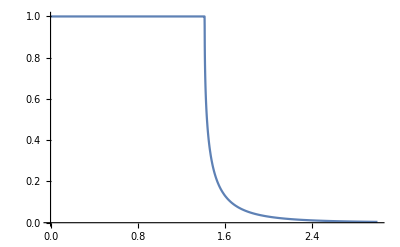

```mathematica
Plot[Abs[(u Cos[θ]-√(-1+u^2 Cos[θ]^2))/(u Cos[θ]+√(-1+u^2 Cos[θ]^2))/.θ->π/4]^2,{u,0,3},PlotRange->All]
```